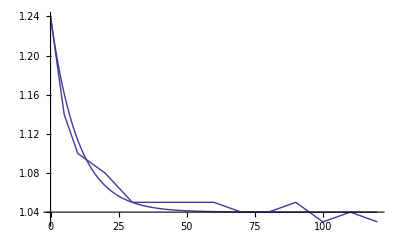

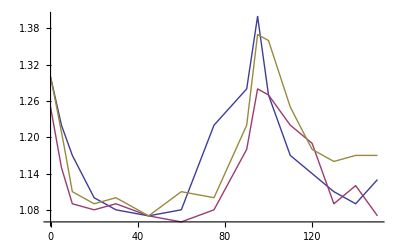

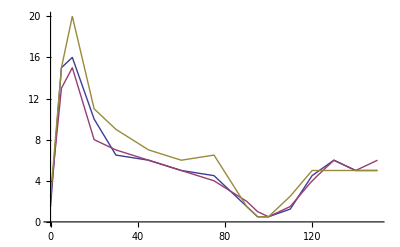

16

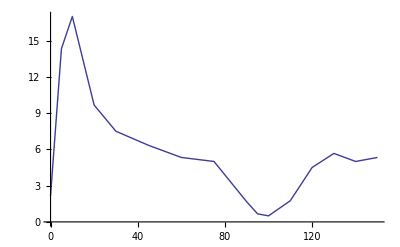

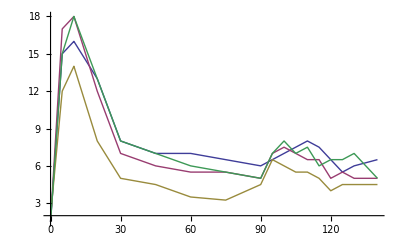

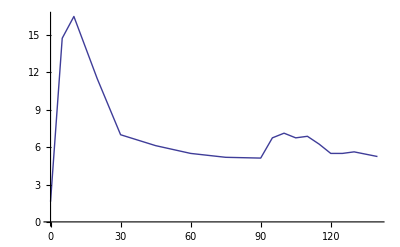

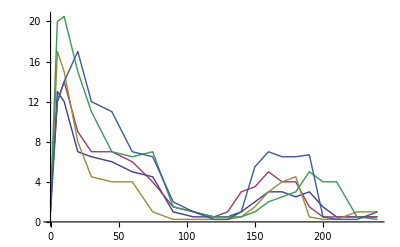

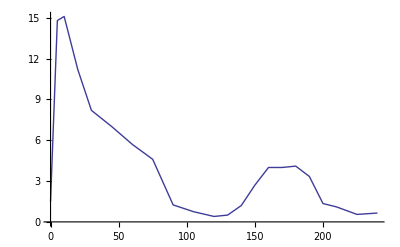

{{1.5,2.5,2.5},{15,13,15},{16,15,20},{10,8,11},{6.5,7,9},{6,6,7},{5,5,6},{4.5,4,6.5},{1.5,2,1.5},{0.5,1,0.5},{0.5,0.5,0.5},{1.25,1.5,2.5},{4.5,4,5},{6,6,5},{5,5,5},{5,6,5}}

{{1.5,1.5,2,1.5},{15,17,12,15},{16,18,14,18},{13,12,8,13},{8,7,5,8},{7,6,4.5,7},{7,5.5,3.5,6},{6.5,5.5,3.25,5.5},{6,5,4.5,5},{6.5,7,6.5,7},{7,7.5,6,8},{7.5,7,5.5,7},{8,6.5,5.5,7.5},{7.5,6.5,5,6},{6.5,5,4,6.5},{5.5,5.5,4.5,6.5},{6,5,4.5,7},{6.5,5,4.5,5}}

{{1.5,2,1,2,1},{13,12,17,20,12},{12,14,15,20.5,14},{7,9,8,15,17},{6.5,7,4.5,11,12},{6,7,4,7,11},{5,6,4,6.5,7},{4.5,4,1,7,6.5},{1,1.5,0.25,1.5,2},{0.5,1,0.25,1,1},{0.5,0.5,0.25,0.5,0.25},{0.5,1,0.25,0.5,0.25},{1,3,0.5,0.5,1},{2,3.5,1.5,1,5.5},{3,5,3,2,7},{3,4,4,2.5,6.5},{2.5,4,4.5,3,6.5},{3,1.5,0.5,5,6.7},{1.5,0.5,0.25,4,0.5},{0.5,0.5,0.25,4,0.25},{0.5,0.5,1,0.5,0.25},{0.5,0.5,1,0.25,1}}

0
1.5 | 5
15 | 10
16 | 20
10 | 30
6.5 | 45
6 | 60
5 | 75
4.5 | 90
1.5 | 95
0.5 | 100
0.5 | 110
1.25 | 120
4.5 | 130
6 | 140
5 | 150
5
0
2.5 | 5
13 | 10
15 | 20
8 | 30
7 | 45
6 | 60
5 | 75
4 | 90
2 | 95
1 | 100
0.5 | 110
1.5 | 120
4 | 130
6 | 140
5 | 150
6
0
2.5 | 5
15 | 10
20 | 20
11 | 30
9 | 45
7 | 60
6 | 75
6.5 | 90
1.5 | 95
0.5 | 100
0.5 | 110
2.5 | 120
5 | 130
5 | 140
5 | 150
5

6.5

1.73205

17.5833

3.16344

47.

7.01427

2.83333

1.75

```mathematica
(*TestValues
3-P[0]/.SolUp
16-P[5]/.SolUp
17.5-P[10]/.SolUp
8-P[30]/.SolUp
3-P[0]/.SolDown
1-P[115]/.SolDown
5.5-P[125]/.SolDown
3-P[150]/.SolDown*)
ClearAll[Ca]

ZeroQ[X_]:=If[X===0,1,-1]
ZL[X_]:=Map[ZeroQ,Sign[X[[1]][[All,2]]-X[[2]][[All,2]]]+Sign[X[[3]][[All,2]]-X[[2]][[All,2]]]]
ZR[X_]:=N[Count[X,1]/Length[X]]

hypoT={0,5,10,20,30,45,60,70,80,90,100,110,120};
HypoCa={1.24,1.14,1.1,1.08,1.05,1.05,1.05,1.04,1.04,1.05,1.03,1.04,1.03};
HypoCaPlus=HypoCa+.05;
HypoCaMinus=HypoCa-.05;
HypoPTH={3.4,16,17,11.5,9,8,7.5,7.75,7.25,7.25,7.5,7.5,7.5};
HypoPTHSD={.1,1,.5,.5,.5,.1,.5,.5,.1,.1,.1,.1,.1};
CaDown=Transpose[{hypoT,HypoCa}];
CaDownPlus=Transpose[{hypoT,HypoCaPlus}];
CaDownMinus=Transpose[{hypoT,HypoCaMinus}];
PTHDown=Transpose[{hypoT,HypoPTH}];
PTHDownPlus=Transpose[{hypoT,HypoPTH+HypoPTHSD}];
PTHDownMinus=Transpose[{hypoT,HypoPTH-HypoPTHSD}];
ca0=HypoCa[[1]];
nds=NDSolve[{Ca'[t]==Piecewise[{{0.1*(ca0-0.2-Ca[t]),t<120}}],Ca[0]==ca0},Ca,{t,0,120}];
Show[Plot[Ca[t]/.nds,{t,0,120},PlotRange->All],ListPlot[CaDown,Joined->True]]

hyperT={0,5,10,15,30,45,60,75,90,115,120,122.5,125,130,140,150,180,210,240};
HyperCa={1.23,1.35,1.4,1.44,1.45,1.46,1.47,1.48,1.47,1.47,1.47,1.38,1.35,1.31,1.28,1.25,1.23,1.23,1.24};
HyperCaPlus=HyperCa+0.05;
HyperCaMinus=HyperCa-0.05;
HyperPTH={3,1.75,1.1,.9,.9,.9,.9,.9,.9,.9,0.9,1.9,4,6,4.5,3,2.5,1.9,2.1};
HyperPTHSD={.5,.1,.1,.1,.1,.1,.1,.1,.1,.1,0.1,.5,1,1,1,1,.5,.5,.1};
CaUp=Transpose[{hyperT,HyperCa}];
CaUpPlus=Transpose[{hyperT,HyperCaPlus}];
CaUpMinus=Transpose[{hyperT,HyperCaMinus}];
PTHUp=Transpose[{hyperT,HyperPTH}];
PTHUpPlus=Transpose[{hyperT,HyperPTH+HyperPTHSD}];
PTHUpMinus=Transpose[{hyperT,HyperPTH-HyperPTHSD}];
SVol=3;


Prot1=Table[{},{index,1,3}];
CaProt1=Table[{},{index,1,3}];
texp1={0,5,10,20,30,45,60,75,90,95,100,110,120,130,140,150};
PexpPmolLong={1.5,15,16,10,6.5,6,5,4.5,1.5,.5,.5,1.25,4.5,6,5,5};
CaLong={1.3,1.22,1.17,1.1,1.08,1.07,1.08,1.22,1.28,1.4,1.27,1.17,1.14,1.11,1.09,1.13};
CaProt1[[1]]=Transpose[{texp1,CaLong}];
Prot1[[1]]=Transpose[{texp1,PexpPmolLong}];
PexpPmolLong={2.5,13,15,8,7,6,5,4,2,1,.5,1.5,4,6,5,6};
CaLong={1.25,1.15,1.09,1.08,1.09,1.07,1.06,1.08,1.18,1.28,1.27,1.22,1.19,1.09,1.12,1.07};
CaProt1[[2]]=Transpose[{texp1,CaLong}];
Prot1[[2]]=Transpose[{texp1,PexpPmolLong}];
PexpPmolLong={2.5,15,20,11,9,7,6,6.5,1.5,.5,.5,2.5,5,5,5,5};
CaLong={1.3,1.21,1.11,1.09,1.1,1.07,1.11,1.1,1.22,1.37,1.36,1.25,1.18,1.16,1.17,1.17};
CaProt1[[3]]=Transpose[{texp1,CaLong}];
Prot1[[3]]=Transpose[{texp1,PexpPmolLong}];
PexpPmolLong={2.5,16,15,7,6,5.5,5,5,3,1,.75,.75,2,4};

ProtCa=Table[Interpolation[CaProt1[[index]],InterpolationOrder->1][t],{index,1,Length[CaProt1]}];
Plot[%,{t,0,150}]
ProtPTH=Table[Interpolation[Prot1[[index]],InterpolationOrder->1][t],{index,1,Length[Prot1]}];
Plot[ProtPTH,{t,0,150}]
lt1=Length[texp1]
PTHMean1=Table[Mean[Transpose[Prot1][[index]]],{index,1,lt1}];
ListPlot[%,Joined->True]


Prot2=Table[{},{index,1,4}];
texp2={0,5,10,20,30,45,60,75,90,95,100,105,110,115,120,125,130,140};
PexpPmolLong={1.5,15,16,13,8,7,7,6.5,6,6.5,7,7.5,8,7.5,6.5,5.5,6,6.5};
Prot2[[1]]=Transpose[{texp2,PexpPmolLong}];
PexpPmolLong={1.5,17,18,12,7,6,5.5,5.5,5,7,7.5,7,6.5,6.5,5,5.5,5,5};
Prot2[[2]]=Transpose[{texp2,PexpPmolLong}];
PexpPmolLong={2,12,14,8,5,4.5,3.5,3.25,4.5,6.5,6,5.5,5.5,5,4,4.5,4.5,4.5};
Prot2[[3]]=Transpose[{texp2,PexpPmolLong}];
PexpPmolLong={1.5,15,18,13,8,7,6,5.5,5,7,8,7,7.5,6,6.5,6.5,7,5};
Prot2[[4]]=Transpose[{texp2,PexpPmolLong}];

ProtPTH=Table[Interpolation[Prot2[[index]],InterpolationOrder->1][t],{index,1,Length[Prot2]}];
Plot[ProtPTH,{t,0,140},PlotRange->All]
lt2=Length[texp2];
PTHMean2=Table[Mean[Transpose[Prot2][[index]]],{index,1,lt2}];
ListPlot[%,Joined->True]

Prot3=Table[{},{index,1,5}];
texp3={0,5,10,20,30,45,60,75,90,105,120,130,140,150,160,170,180,190,200,210,225,240};
PexpPmolLong={1.5,13,12,7,6.5,6,5,4.5,1,.5,.5,.5,1,2,3,3,2.5,3,1.5,.5,.5,.5};
Prot3[[1]]=Transpose[{texp3,PexpPmolLong}];
PexpPmolLong={2,12,14,9,7,7,6,4,1.5,1,.5,1,3,3.5,5,4,4,1.5,.5,.5,.5,.5};
Prot3[[2]]=Transpose[{texp3,PexpPmolLong}];
PexpPmolLong={1,17,15,8,4.5,4,4,1,.25,.25,.25,.25,.5,1.5,3,4,4.5,.5,.25,.25,1,1};
Prot3[[3]]=Transpose[{texp3,PexpPmolLong}];
PexpPmolLong={2,20,20.5,15,11,7,6.5,7,1.5,1,.5,.5,.5,1,2,2.5,3,5,4,4,.5,.25};
Prot3[[4]]=Transpose[{texp3,PexpPmolLong}];
PexpPmolLong={1,12,14,17,12,11,7,6.5,2,1,.25,.25,1,5.5,7,6.5,6.5,6.7,.5,.25,.25,1};
Prot3[[5]]=Transpose[{texp3,PexpPmolLong}];

ProtPTH3=Table[Interpolation[Prot3[[index]],InterpolationOrder->1][t],{index,1,Length[Prot3]}];
Plot[%,{t,0,240}]
lt3=Length[texp3];
PTHMean3=Table[Mean[Transpose[Prot3][[index]]],{index,1,lt3}];
ListPlot[%,Joined->True]
(*{kv,kd,kdeg,beta,gamma,m,frac,delay,TestSum}*)

P1Exp=Transpose[Prot1][[All,All,2]]
P2Exp=Transpose[Prot2][[All,All,2]]
P3Exp=Transpose[Prot3][[All,All,2]]
TestCI[x_,y_]:=If[x[[1]]≤y≤x[[2]],1,0];
TestLow[x_,y_]:=If[x[[1]]>y,1,0];
F1[ci_,testci_,i_]:=Map[TestCI[ci[[i]],#]&,testci[[i]]];
F2[ci_,testci_,i_]:=Map[TestLow[ci[[i]],#]&,testci[[i]]];

TableForm[Prot1]
BLm=3*Mean[Prot1[[All,1]][[All,2]]]
BLsd=3*StandardDeviation[Prot1[[All,1]][[All,2]]]
hypom=3*Mean[Flatten[Prot1[[All,{5,6,7,14,15,16}]][[All,All,2]]]]
hyposd=3*StandardDeviation[Flatten[Prot1[[All,{5,6,7,14,15,16}]][[All,All,2]]]]
hystm=3*N[Mean[Flatten[Prot1[[All,{2,3}]][[All,All,2]]]]]
hystsd=3*N[StandardDeviation[Flatten[Prot1[[All,{2,3}]][[All,All,2]]]]]
hyperm=3*Mean[Flatten[Prot1[[All,{9,10,11}]][[All,All,2]]]]
hypersd=3*StandardDeviation[Flatten[Prot1[[All,{9,10,11}]][[All,All,2]]]]
```

```mathematica
(* this subroutine establishes the experimental distributions*)
ClearAll[kv1,kv2,m1,m2,kd1,kd2,gammac,gamma,beta,kdeg,OutTest]
x=1.27
SVol=3;
ECFV=11;
kcl=0.6613/SVol;

sdlist={BLsd,hyposd,hypersd,hystsd}
mlist={BLm,hypom,hyperm,hystm}

Outputs={NormalDistribution[mlist[[1]],sdlist[[1]]],NormalDistribution[mlist[[2]],sdlist[[2]]],NormalDistribution[mlist[[3]],sdlist[[3]]],NormalDistribution[mlist[[4]],sdlist[[4]]]}
(*OutTest is essentially a z-score in each dimension, considered independently*)
OutTest[{x_,y_,z_,w_}]:={(mlist[[1]]-x)/sdlist[[1]],(mlist[[2]]-y)/sdlist[[2]],(mlist[[3]]-z)/sdlist[[3]],(mlist[[4]]-w)/sdlist[[4]]}
nd=RandomVariate[NormalDistribution[],{1000}];
model=Sort[Table[Map[RandomVariate,Outputs],{10000}]];
outputs=Map[OutTest[#]&,model];
```

1.27

{1.73205,3.16344,1.75,7.01427}

{6.5,17.5833,2.83333,47.}

{NormalDistribution[6.5,1.73205],NormalDistribution[17.5833,3.16344],NormalDistribution[2.83333,1.75],NormalDistribution[47.,7.01427]}

```mathematica
(*Pssi establishes steady state behavior for each type of cell*)
Pss1[x_]:=(SVol/0.6613)*(kv1)*(beta-gamma*x^m1/(x^m1+kd1^m1))/(kdeg+beta-gamma*x^m1/(x^m1+kd1^m1));
Pss2[x_]:=(SVol/0.6613)*(kv2)*(beta-gamma*x^m2/(x^m2+kd2^m2))/(kdeg+beta-gamma*x^m2/(x^m2+kd2^m2));
Pss[x_]:=(Pss1[x]+Pss2[x]);

(*initialilzing distributions*)
DA1=UniformDistribution[{1,10}];(*3.5*)
Dkd1=UniformDistribution[{1.025,1.175}];
Dm1=UniformDistribution[{100,400}];
DA2=UniformDistribution[{1,10}];(*1.5*)
Dkd2=UniformDistribution[{1.2,1.35}];
Dm2=UniformDistribution[{100,400}];
DGc=UniformDistribution[{0.00005,0.0025}];
DB=UniformDistribution[{0.1,0.9}]

Dists0={DA1,Dkd1,Dm1,DA2,Dkd2,Dm2,DGc,DB}
Dists=Dists0;
(*The "Values" module is the workhorse of the solution; it is executed "number" times generating the individuals who comprise the in silico model*)
Values[z_,number_]:=Do[
(*Samples distributions*)
kv1=RandomVariate[z[[1]]];
kd1=RandomVariate[z[[2]]];
m1=RandomVariate[z[[3]]];
kv2=RandomVariate[z[[4]]];
kd2=RandomVariate[z[[5]]];
m2=RandomVariate[z[[6]]];
gammac=RandomVariate[z[[7]]];
beta=RandomVariate[z[[8]]];
gamma=beta-gammac;
kdeg=0.02;(*0.02 comes from Morrissey and Cohn 1979*)(*0.0075*)
AppendTo[PV,{kv1,kd1,m1,kv2,kd2,m2,gammac,beta}];
(*define the calcium profile with stochastic fluctuations*)
CaList={RandomReal[NormalDistribution[1.27,0.03]],RandomReal[NormalDistribution[1.07,0.03]],RandomReal[NormalDistribution[1.47,0.04]]};
ca0=CaList[[1]];
(*solve the differential system numerically*)
SolDown=NDSolve[{
SF1[t]==beta-(gamma*Ca[t]^m1/(Ca[t]^m1+kd1^m1)),
SF2[t]==beta-(gamma*Ca[t]^m2/(Ca[t]^m2+kd2^m2)),
P'[t]==(SF1[t]*V1[t]+SF2[t]*V2[t])-(kcl*P[t])-EP'[t],
P[0]==(kv1/kcl)*(beta-gamma*ca0^m1/(ca0^m1+kd1^m1))/(kdeg+beta-gamma*ca0^m1/(ca0^m1+kd1^m1))+(kv2/kcl)*(beta-gamma*ca0^m2/(ca0^m2+kd2^m2))/(kdeg+beta-gamma*ca0^m2/(ca0^m2+kd2^m2)),
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),
EP[0]==(11/SVol)*P[0],
V1'[t]==kv1-(kdeg+SF1[t])*V1[t],
V2'[t]==kv2-(kdeg+SF2[t])*V2[t],
V1[0]==(kv1/((beta+kdeg-gamma*(ca0^m1)/(ca0^m1+kd1^m1)))),
V2[0]==(kv2/((beta+kdeg-gamma*(ca0^m2)/(ca0^m2+kd2^m2)))),
Ca'[t]==Piecewise[{{0.1*(ca0-0.2-Ca[t]),t<120}}],
Ca[0]==ca0},
{P,Ca,V1,V2,EP,SF1,SF2},{t,0,10}][[1]];
AppendTo[model,{Pss[CaList[[1]]],Pss[CaList[[2]]],Pss[CaList[[3]]],P[10]/.SolDown}],{number}]

(*initial test*)
(* 5000 runs to determine initial output distributions; these will be jack-knifed to form the next iteration of parameter distributions*)
model={};
PV={};
Values[Dists,5000];
outputs=Map[OutTest[#]&,model];
NormalCheck=Table[Abs[Mean[outputs[[All,i]]]],{i,1,4}];
ADTest=Apply[Times,NormalCheck];
MaxTest=Max[NormalCheck];
Print[NormalCheck,"  ",ADTest,"   ",MaxTest];
counter=0;

(*calibration loop*)
(*this is the iterative part of the construction.  the loop will run until the average z-scor across the four measured components is <0.5, and the worst z-score is 1.5*)
(*the counter is to prevent infinite looping, but does not practically get invoked*)
While[(ADTest>0.5||MaxTest>1.5)&&counter<100,
counter++;
Probs=outputs;
closelist=Select[Probs,-2<Min[#]<Max[#]<2&];
Print[Length[closelist]];
closepositions=Flatten[Map[Position[Probs,#]&,closelist]];
close=PV[[closepositions]];
tc=Transpose[close];
tm=Transpose[PV];
Dists=Table[SmoothKernelDistribution[tc[[k]]],{k,1,8}];
model={};
PV={};
Values[Dists,2000];
outputs=Map[OutTest[#]&,model];
NormalCheck=Table[Abs[Mean[outputs[[All,i]]]],{i,1,4}];
ADTest=Apply[Times,NormalCheck];
MaxTest=Max[NormalCheck];
Print[NormalCheck,"  ",ADTest,"   ",MaxTest];
Print[ADTest>0.5," ",MaxTest>2," ",counter<100,"   ",((ADTest>0.25)||(MaxTest>1))&&(counter<100)]];

TableForm[Table[Mean[model[[All,i]]],{i,1,Length[model[[1]]]}]]
TableForm[Table[Mean[PV[[All,i]]],{i,1,Length[PV[[1]]]}]]
ADTest
MaxTest
```

UniformDistribution[{0.1,0.9}]

{UniformDistribution[{1,10}],UniformDistribution[{1.025,1.175}],UniformDistribution[{100,400}],UniformDistribution[{1,10}],UniformDistribution[{1.2,1.35}],UniformDistribution[{100,400}],UniformDistribution[{0.00005,0.0025}],UniformDistribution[{0.1,0.9}]}

{5.98216,7.80422,0.0645392,1.23656}  3.72586   7.80422

40

{0.453424,3.96827,0.530196,0.622104}  0.59348   3.96827

True True True   True

44

{0.396447,1.49953,0.601452,1.07754}  0.385281   1.49953

False False True   True

7.18667
22.327
1.78079
39.4418

3.57144
1.13358
267.027
2.14519
1.27132
244.427
0.00146181
0.497736

0.385281

1.49953

{DataDistribution[«SmoothKernel»,{44}],DataDistribution[«SmoothKernel»,{44}],DataDistribution[«SmoothKernel»,{44}],DataDistribution[«SmoothKernel»,{44}],DataDistribution[«SmoothKernel»,{44}],DataDistribution[«SmoothKernel»,{44}],DataDistribution[«SmoothKernel»,{44}],DataDistribution[«SmoothKernel»,{44}]}

{3.0714,1.00311,133.979,1.85136,1.29379,259.479,0.00169948,0.362462}

{3.57144,1.13358,267.027,2.14519,1.27132,244.427,0.00146181,0.497736}

{1.89663,0.0561335,101.679,1.40519,0.0506239,92.1356,0.000613645,0.255569}

{3.57144,1.89663}

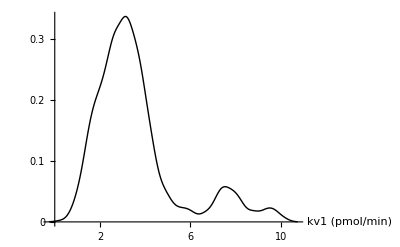

{1.13358,0.0561335}

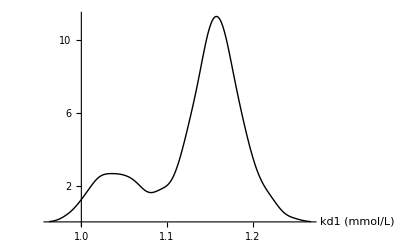

{267.027,101.679}

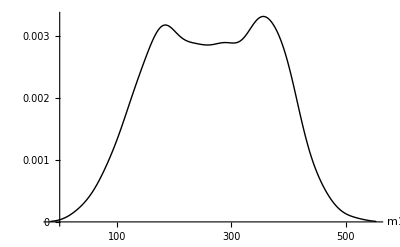

{2.14519,1.40519}

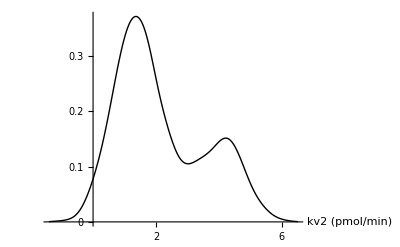

{1.27132,0.0506239}

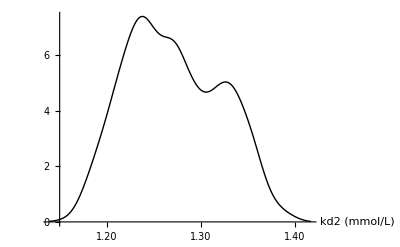

{244.427,92.1356}

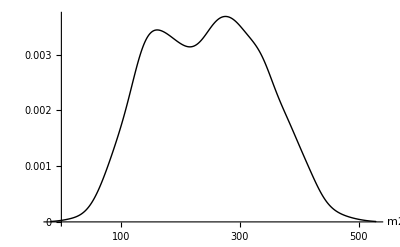

{0.00146181,0.000613645}

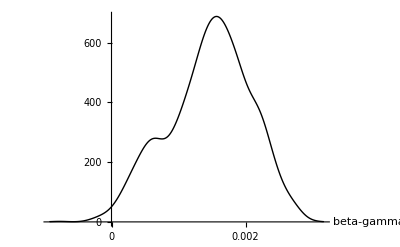

{0.497736,0.255569}

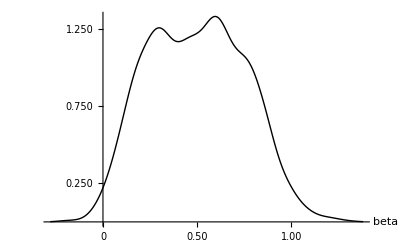

```mathematica
(*demonstrate the calibrated parameter distributions*)
{KV1,KD1,M1,KV2,KD2,M2,GAMMAC,BETA}=Dists
{kv1,kd1,m1,kv2,kd2,m2,gammac,beta}=Table[RandomVariate[Dists[[i]]],{i,1,Length[Dists]}]

Map[Mean,Transpose[PV]]
Map[StandardDeviation,Transpose[PV]]

Print[{Mean[PV[[All,1]]],StandardDeviation[PV[[All,1]]]}]
SmoothHistogram[Flatten[PV[[All,1]]],PlotStyle->Black,AxesLabel->{"kv1 (pmol/min)",""}]
Print[{Mean[PV[[All,2]]],StandardDeviation[PV[[All,2]]]}]
SmoothHistogram[Flatten[PV[[All,2]]],PlotStyle->Black,AxesLabel->{"kd1 (mmol/L)",""}]
Print[{Mean[PV[[All,3]]],StandardDeviation[PV[[All,3]]]}]
SmoothHistogram[Flatten[PV[[All,3]]],PlotStyle->Black,AxesLabel->{"m1 ",""}]
Print[{Mean[PV[[All,4]]],StandardDeviation[PV[[All,4]]]}]
SmoothHistogram[Flatten[PV[[All,4]]],PlotStyle->Black,AxesLabel->{"kv2 (pmol/min)",""}]
Print[{Mean[PV[[All,5]]],StandardDeviation[PV[[All,5]]]}]
SmoothHistogram[Flatten[PV[[All,5]]],PlotStyle->Black,AxesLabel->{"kd2 (mmol/L)",""}]
Print[{Mean[PV[[All,6]]],StandardDeviation[PV[[All,6]]]}]
SmoothHistogram[Flatten[PV[[All,6]]],PlotStyle->Black,AxesLabel->{"m2 ",""}]
Print[{Mean[PV[[All,7]]],StandardDeviation[PV[[All,7]]]}]
SmoothHistogram[Flatten[PV[[All,7]]],PlotStyle->Black,AxesLabel->{"beta-gamma",""}]
Print[{Mean[PV[[All,8]]],StandardDeviation[PV[[All,8]]]}]
SmoothHistogram[Flatten[PV[[All,8]]],PlotStyle->Black,AxesLabel->{"beta ",""}]
```

```mathematica
(*this submodule generates the individuals and their response curves*)
(* each individual is comprised of 20 pairs of models (kv1 vs kv2 etc)*)

ClearAll[GenerateCurves];
TestMin=0;
{KV1,KD1,M1,KV2,KD2,M2,GAMMAC,BETA}=Dists;
GenerateCurves[ind_]:=Do[
PUtot={};
PDtot={};
P1tot={};
P2tot={};
P3tot={};
PV={};
SolDown={};
SolUp={};
Sol1={};
Sol2={};
Sol3={};
Do[
MaxRuns=20;
AppendTo[SolDown,{}];
AppendTo[SolUp,{}];
AppendTo[Sol1,{}];
AppendTo[Sol2,{}];
AppendTo[Sol3,{}];
AppendTo[PV,{}];
Do[
(*Sample*)
trialvec=Table[RandomVariate[Dists[[i]]],{i,1,Length[Dists]}];
While[Min[trialvec]<=0,
trialvec=Table[RandomVariate[Dists[[i]]],{i,1,Length[Dists]}]];
{kv1,kd1,m1,kv2,kd2,m2,gammac,beta}=trialvec;
gamma=beta-gammac;
AppendTo[PV[[-1]],{kv1,kd1,m1,kv2,kd2,m2,gammac,beta}];
ca0=1.27;
(*SolDown is a hypocalcemia protocol*)
AppendTo[SolDown[[-1]],NDSolve[{
SF1[t]==beta-(gamma*Ca[t]^m1/(Ca[t]^m1+kd1^m1)),
SF2[t]==beta-(gamma*Ca[t]^m2/(Ca[t]^m2+kd2^m2)),
P'[t]==(SF1[t]*V1[t]+SF2[t]*V2[t])-(kcl*P[t])-EP'[t],
P[0]==(kv1/kcl)*(beta-gamma*ca0^m1/(ca0^m1+kd1^m1))/(kdeg+beta-gamma*ca0^m1/(ca0^m1+kd1^m1))+(kv2/kcl)*(beta-gamma*ca0^m2/(ca0^m2+kd2^m2))/(kdeg+beta-gamma*ca0^m2/(ca0^m2+kd2^m2)),
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),
EP[0]==(11/SVol)*P[0],
V1'[t]==kv1-(kdeg+SF1[t])*V1[t],
V2'[t]==kv2-(kdeg+SF2[t])*V2[t],
V1[0]==(kv1/((beta+kdeg-gamma*(ca0^m1)/(ca0^m1+kd1^m1)))),
V2[0]==(kv2/((beta+kdeg-gamma*(ca0^m2)/(ca0^m2+kd2^m2)))),
Ca'[t]==Piecewise[{{0.1*(ca0-0.2-Ca[t]),t<120}}],Ca[0]==ca0},
{P,Ca,V1,V2,EP,SF1,SF2},{t,0,120}][[1]]];
(*SolUp is a hypercalcemia protocol*)
AppendTo[SolUp[[-1]],NDSolve[{
SF1[t]==beta-(gamma*Ca[t]^m1/(Ca[t]^m1+kd1^m1)),
SF2[t]==beta-(gamma*Ca[t]^m2/(Ca[t]^m2+kd2^m2)),
P'[t]==(SF1[t]*V1[t]+SF2[t]*V2[t])-(kcl*P[t])-EP'[t],
P[0]==(kv1/kcl)*(beta-gamma*ca0^m1/(ca0^m1+kd1^m1))/(kdeg+beta-gamma*ca0^m1/(ca0^m1+kd1^m1))+(kv2/kcl)*(beta-gamma*ca0^m2/(ca0^m2+kd2^m2))/(kdeg+beta-gamma*ca0^m2/(ca0^m2+kd2^m2)),
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),
EP[0]==(11/SVol)*P[0],
V1'[t]==kv1-(kdeg+SF1[t])*V1[t],
V2'[t]==kv2-(kdeg+SF2[t])*V2[t],
V1[0]==(kv1/((beta+kdeg-gamma*(ca0^m1)/(ca0^m1+kd1^m1)))),
V2[0]==(kv2/((beta+kdeg-gamma*(ca0^m2)/(ca0^m2+kd2^m2)))),
Ca'[t]==Piecewise[{{0.125*(ca0+0.2-Ca[t]),t≤120},{0.1*(ca0+.015-Ca[t]),t<240}}],Ca[0]==ca0},
{P,Ca,V1,V2,EP,SF1,SF2},{t,0,240}]];
(*this is the first validation protocol*)
AppendTo[Sol1[[-1]],NDSolve[{
SF1[t]==beta-(gamma*Ca[t]^m1/(Ca[t]^m1+kd1^m1)),
SF2[t]==beta-(gamma*Ca[t]^m2/(Ca[t]^m2+kd2^m2)),
P'[t]==(SF1[t]*V1[t]+SF2[t]*V2[t])-(kcl*P[t])-EP'[t],
P[0]==(kv1/kcl)*(beta-gamma*ca0^m1/(ca0^m1+kd1^m1))/(kdeg+beta-gamma*ca0^m1/(ca0^m1+kd1^m1))+(kv2/kcl)*(beta-gamma*ca0^m2/(ca0^m2+kd2^m2))/(kdeg+beta-gamma*ca0^m2/(ca0^m2+kd2^m2)),
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),
EP[0]==(11/SVol)*P[0],
V1'[t]==kv1-(kdeg+SF1[t])*V1[t],
V2'[t]==kv2-(kdeg+SF2[t])*V2[t],
V1[0]==(kv1/((beta+kdeg-gamma*(ca0^m1)/(ca0^m1+kd1^m1)))),
V2[0]==(kv2/((beta+kdeg-gamma*(ca0^m2)/(ca0^m2+kd2^m2)))),
Ca'[t]==Piecewise[{{0.22*(ca0-.2-Ca[t]),t<75},{.15*(ca0+0.05-Ca[t]),t<105},{0.07*(1.05-Ca[t]),True}}],Ca[0]==ca0},
{P,Ca,V1,V2,EP,SF1,SF2},{t,0,150}]];
(*This is the second validation protocol*)
AppendTo[Sol2[[-1]],NDSolve[{
SF1[t]==beta-(gamma*Ca[t]^m1/(Ca[t]^m1+kd1^m1)),
SF2[t]==beta-(gamma*Ca[t]^m2/(Ca[t]^m2+kd2^m2)),
P'[t]==(SF1[t]*V1[t]+SF2[t]*V2[t])-(kcl*P[t])-EP'[t],
P[0]==(kv1/kcl)*(beta-gamma*ca0^m1/(ca0^m1+kd1^m1))/(kdeg+beta-gamma*ca0^m1/(ca0^m1+kd1^m1))+(kv2/kcl)*(beta-gamma*ca0^m2/(ca0^m2+kd2^m2))/(kdeg+beta-gamma*ca0^m2/(ca0^m2+kd2^m2)),
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),
EP[0]==(11/SVol)*P[0],
V1'[t]==kv1-(kdeg+SF1[t])*V1[t],
V2'[t]==kv2-(kdeg+SF2[t])*V2[t],
V1[0]==(kv1/((beta+kdeg-gamma*(ca0^m1)/(ca0^m1+kd1^m1)))),
V2[0]==(kv2/((beta+kdeg-gamma*(ca0^m2)/(ca0^m2+kd2^m2)))),
Ca'[t]==Piecewise[{{0.15*(1.05-Ca[t]),t<90},{.1*(0.85-Ca[t]),t<150}}],Ca[0]==ca0},
{P,Ca,V1,V2,EP,SF1,SF2},{t,0,150}]];
(*This is the protocol which was used to generate the 4 data families used for calibration.  It is included for completeness*)
AppendTo[Sol3[[-1]],NDSolve[{
SF1[t]==beta-(gamma*Ca[t]^m1/(Ca[t]^m1+kd1^m1)),
SF2[t]==beta-(gamma*Ca[t]^m2/(Ca[t]^m2+kd2^m2)),
P'[t]==(SF1[t]*V1[t]+SF2[t]*V2[t])-(kcl*P[t])-EP'[t],
P[0]==(kv1/kcl)*(beta-gamma*ca0^m1/(ca0^m1+kd1^m1))/(kdeg+beta-gamma*ca0^m1/(ca0^m1+kd1^m1))+(kv2/kcl)*(beta-gamma*ca0^m2/(ca0^m2+kd2^m2))/(kdeg+beta-gamma*ca0^m2/(ca0^m2+kd2^m2)),
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),
EP[0]==(11/SVol)*P[0],
V1'[t]==kv1-(kdeg+SF1[t])*V1[t],
V2'[t]==kv2-(kdeg+SF2[t])*V2[t],
V1[0]==(kv1/((beta+kdeg-gamma*(ca0^m1)/(ca0^m1+kd1^m1)))),
V2[0]==(kv2/((beta+kdeg-gamma*(ca0^m2)/(ca0^m2+kd2^m2)))),
Ca'[t]==Piecewise[{{0.175*(ca0-0.2-Ca[t]),t<75},{.075*(ca0+0.2-Ca[t]),75<=t<130},{.075*(ca0-0.12-Ca[t]),t<180},{.1*(ca0+0.2-Ca[t]),True}}],Ca[0]==ca0},
{P,Ca,V1,V2,EP,SF1,SF2},{t,0,240}]],
{MaxRuns}]
,{ind}],{1}]

(*this submodule process confidence intervals*)

ProcessCI:=Do[
C95={};
C50={};
dx=0.025;
ExperimentList={PUtot,PDtot,P1tot,P2tot,P3tot};
Mn={};
Do[
LN=ExperimentList[[index]];
CInv95={};
CInv50={};
Do[
elt=Transpose[LN][[j]];
bc=BinCounts[elt,dx];
BL=BinLists[elt,dx];
lbc=Apply[Plus,bc];
frac=Table[0,{Length[bc]}];
cntr=0;
For[i=1,i≤Floor[Length[bc]/2],i++,
cntr=cntr+Apply[Plus,bc[[{i,-i}]]];
frac[[i]]=N[cntr/lbc]];
Bad95=Union[Select[frac,(#<0.025)||(#>0.975)&]];
BadSet95=Flatten[Map[Position[frac,#]&,Bad95],1];
Bad50=Union[Select[frac,(#<0.25)||(#>0.75)&]];
BadSet50=Flatten[Map[Position[frac,#]&,Bad50],1];
CI95=Flatten[Delete[BL,BadSet95]][[{1,-1}]];
CI50=Flatten[Delete[BL,BadSet50]][[{1,-1}]];
AppendTo[CInv95,CI95];
AppendTo[CInv50,CI50],{j,1,Length[LN[[1]]]}];
AppendTo[C95,CInv95];
AppendTo[C50,CInv50];
AppendTo[Mn,Map[Mean,Transpose[LN]]],{index,1,5}];
{CIUv95,CIDv95,CI1v95,CI2v95,CI3v95}=C95;
{CIUv50,CIDv50,CI1v50,CI2v50,CI3v50}=C50,{1}]

(*This module generates confidence intervals and charts dynamic behavior*)
(*This is done by selecting the middle 95% interval from the cumulative distribution function for each output point (CI[y,L] (i.e. this is an independent/uncorrelated CI*)
(*dynamic behavior is up/down.stationary behavior between adjact points (DynObs[x]*)
CIgenerator:=Do[
CI[y_,L_]:=Do[
distz=SmoothKernelDistribution[y];
icdfz[X_]:=InverseCDF[distz,X];
Return[{icdfz[L/2],icdfz[1-(L/2)]}],{1}];
DynObs[x_]:=
If[Length[x]<=1,
0,
Table[Sign[x[[i]]-x[[i-1]]],{i,2,Length[x]}]];
RawPerformance[p_,c_]:=Flatten[Table[BinCounts[p[[j]],c[[j]]],{j,1,Length[p]}]];
Performance[p_,c_]:=N[Apply[Plus,Flatten[Table[BinCounts[p[[j]],c[[j]]],{j,1,Length[p]}]]]/Length[Flatten[p]]];

P1f=Transpose[Flatten[P1,1]/.t->texp1];
P2f=Transpose[Flatten[P2,1]/.t->texp2];
Sol1Mean=Map[Mean,Transpose[Table[Map[Mean,Transpose[Flatten[((P[t]/SVol)/.Sol1[[i]]/.t->texp1),1]]],{i,1,Length[Sol1]}]]];
Sol2Mean=Map[Mean,Transpose[Table[Map[Mean,Transpose[Flatten[((P[t]/SVol)/.Sol2[[i]]/.t->texp2),1]]],{i,1,Length[Sol2]}]]];

CI1=Map[CI[#,0.05]&,P1f];
CI1forBins=Table[Join[CI1[[i]],{CI1[[i,2]]-CI1[[i,1]]}],{i,1,Length[CI1]}];(*produces list of "low, high, and width"*)
Prot1PTH=Transpose[Prot1[[All,All,2]]];
CI2=Map[CI[#,0.05]&,P2f];
CI2forBins=Table[Join[CI2[[i]],{CI2[[i,2]]-CI2[[i,1]]}],{i,1,Length[CI2]}];
Prot2PTH=Transpose[Prot2[[All,All,2]]];

Print["1"];
Print[Performance[Prot1PTH,CI1forBins]];
DynSeq[a_,b_]:=DynObs[a]-Mean[Map[DynObs,Transpose[b]]];
Print[DynSeq[Sol1Mean,Prot1PTH]];
Print["2"];
(*Print[RawPerformance[Prot2PTH,CI2forBins]];*)
Print[Performance[Prot2PTH,CI2forBins]];


Print[DynObs[Sol2Mean]-Mean[Map[DynObs,Transpose[Prot2PTH]]]],{1}];
```

```mathematica
(*This is the data production submodule*)
(*The calibrated parameters are used to Generate 25 individuals (GenerateCurves)*)
(*Outputs are tabled, and confidence intervals are generated (CIGenerator) *)
(*Percentage of behavior within lilmits is displayed as well as the dynamic observations (up/down/stationary) *)
list1={};
list2={};
path="C:\\Documents and Settings\\Hester_lab\\My Documents\\";
Do[
GenerateCurves[25];
PDown=Table[Mean[(P[t]/SVol)/.SolDown[[i]]],{i,1,Length[SolDown]}];
PUp=Table[Mean[(P[t]/SVol)/.SolUp[[i]]],{i,1,Length[SolUp]}];
P1=Table[Mean[(P[t]/SVol)/.Sol1[[i]]],{i,1,Length[Sol1]}];
P2=Table[Mean[(P[t]/SVol)/.Sol2[[i]]],{i,1,Length[Sol2]}];
P3=Table[Mean[(P[t]/SVol)/.Sol3[[i]]],{i,1,Length[Sol3]}];

CIgenerator;
AppendTo[list1,Performance[Prot1PTH,CI1forBins]];
AppendTo[list2,Performance[Prot2PTH,CI2forBins]];
Print[],{1}]
```

1

0.354167

{0,-2,0,0,0,0,-2/3,0,0,-2/3,0,0,-5/3,-1/3,-4/3}

2

0.486111

{0,0,0,0,0,-1/4,-1/4,-1/2,0,-3/2,-1/2,-5/4,-1/4,-1/2,-5/4,-5/4,-1}

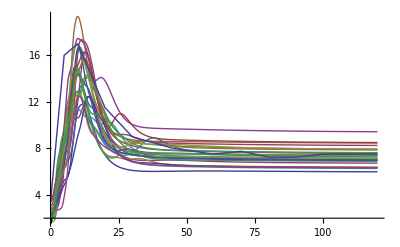

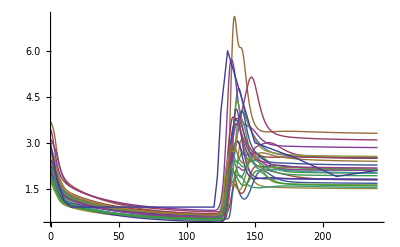

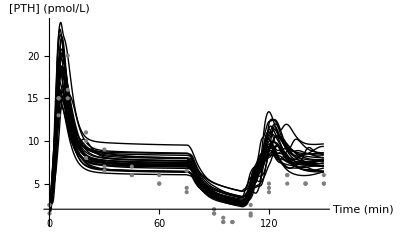

C:\Documents and Settings\Hester_lab\My Documents\Prot1.jpg

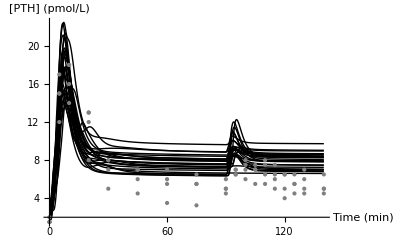

C:\Documents and Settings\Hester_lab\My Documents\Prot2.jpg

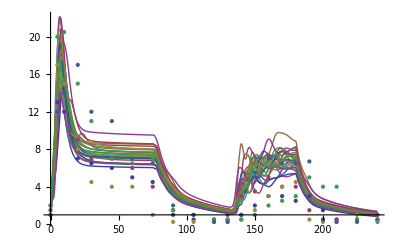

```mathematica
(*Curve families are plotted*)
Table[Mean[PV[[All,i]]],{i,1,Length[PV[[1]]]}];
Show[Plot[PDown,{t,0,120},PlotRange->All],ListPlot[PTHDown,Joined->True]]
Show[Plot[PUp,{t,0,240},PlotRange->All],ListPlot[PTHUp,Joined->True]]

Show[Plot[P1,{t,0,150},PlotRange->All,PlotStyle->Black,AxesLabel->{"Time (min)","[PTH] (pmol/L)"},Ticks->{{0,30,60,90,120,150},Automatic}],ListPlot[Prot1,PlotStyle->{{Gray,PointSize[Large]}}]]
Export[path<>"Prot1.jpg",%]
Show[Plot[P2,{t,0,140},PlotRange->All,PlotStyle->Black,AxesLabel->{"Time (min)","[PTH] (pmol/L)"},Ticks->{{0,30,60,90,120,140},Automatic}],ListPlot[Prot2,PlotStyle->{{Gray,PointSize[Large]}}]]
Export[path<>"Prot2.jpg",%]
Show[Plot[P3,{t,0,240},PlotRange->All],ListPlot[Prot3]]
```

```mathematica
Export[path<>"P1.xlsx",Transpose[Prepend[(P1/.t->texp1)[[All,1]],texp1]]]
Export[path<>"P2.xlsx",Transpose[Prepend[(P2/.t->texp2)[[All,1]],texp2]]]
```

C:\Documents and Settings\Hester_lab\My Documents\P1.xlsx

C:\Documents and Settings\Hester_lab\My Documents\P2.xlsx

```mathematica
Prot1xlsx=Join[{Prot1[[All,All,1]][[1]]},Table[Prot1[[All,All,2]][[i]],{i,1,Length[Prot1]}]]
Prot2xlsx=Join[{Prot2[[All,All,1]][[1]]},Table[Prot2[[All,All,2]][[i]],{i,1,Length[Prot2]}]]
Export[path<>"Prot1.xlsx",Transpose[Prot1xlsx]]
Export[path<>"Prot2.xlsx",Transpose[Prot2xlsx]]
```

{{0,5,10,20,30,45,60,75,90,95,100,110,120,130,140,150},{1.5,15,16,10,6.5,6,5,4.5,1.5,0.5,0.5,1.25,4.5,6,5,5},{2.5,13,15,8,7,6,5,4,2,1,0.5,1.5,4,6,5,6},{2.5,15,20,11,9,7,6,6.5,1.5,0.5,0.5,2.5,5,5,5,5}}

{{0,5,10,20,30,45,60,75,90,95,100,105,110,115,120,125,130,140},{1.5,15,16,13,8,7,7,6.5,6,6.5,7,7.5,8,7.5,6.5,5.5,6,6.5},{1.5,17,18,12,7,6,5.5,5.5,5,7,7.5,7,6.5,6.5,5,5.5,5,5},{2,12,14,8,5,4.5,3.5,3.25,4.5,6.5,6,5.5,5.5,5,4,4.5,4.5,4.5},{1.5,15,18,13,8,7,6,5.5,5,7,8,7,7.5,6,6.5,6.5,7,5}}

C:\Documents and Settings\Hester_lab\My Documents\Prot1.xlsx

C:\Documents and Settings\Hester_lab\My Documents\Prot2.xlsx

```mathematica
(*data details*)
prot=Prot1PTH;
sol=Sol1Mean;
DynObs[N[Mean[Transpose[prot]]]]
DynObs[sol]
DynObs[N[Mean[Transpose[prot]]]]-DynObs[sol]
TableForm[{sol,N[Mean[Transpose[prot]]],DynObs[N[Mean[Transpose[prot]]]]-DynObs[sol]}]
Print[]
prot=Prot2PTH;
sol=Sol2Mean;
DynObs[N[Mean[Transpose[prot]]]]
DynObs[sol]
DynObs[N[Mean[Transpose[prot]]]]-DynObs[sol]
TableForm[{sol,N[Mean[Transpose[prot]]],DynObs[N[Mean[Transpose[prot]]]]-DynObs[sol]}]
```

{1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,1}

{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1,-1,1}

{0,2,0,0,0,0,0,0,0,0,0,0,2,0,0}

2.51919 | 17.0409 | 14.586 | 8.49928 | 7.86605 | 7.67566 | 7.59878 | 7.55107 | 3.9239 | 3.46868 | 3.17067 | 4.80252 | 9.82992 | 8.55787 | 7.77136 | 7.82152
2.16667 | 14.3333 | 17. | 9.66667 | 7.5 | 6.33333 | 5.33333 | 5. | 1.66667 | 0.666667 | 0.5 | 1.75 | 4.5 | 5.66667 | 5. | 5.33333
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 |

{1,1,-1,-1,-1,-1,-1,-1,1,1,-1,1,-1,-1,0,1,-1}

{1,1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1}

{0,0,0,0,0,0,0,0,0,2,0,2,0,0,1,2,0}

2.51919 | 14.0037 | 15.5609 | 9.03884 | 8.30241 | 7.96653 | 7.86961 | 7.81405 | 7.77769 | 9.70087 | 8.71845 | 8.37014 | 8.27998 | 8.25042 | 8.23596 | 8.22626 | 8.21863 | 8.20671
1.625 | 14.75 | 16.5 | 11.5 | 7. | 6.125 | 5.5 | 5.1875 | 5.125 | 6.75 | 7.125 | 6.75 | 6.875 | 6.25 | 5.5 | 5.5 | 5.625 | 5.25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 1 | 2 | 0 |

```mathematica
(*fitted model; standard sigmoid (Brown) to average data in hypo-, hyper- and normocalcemia*)
data=Transpose[{(Ca[t]/.Sol3[[1]][[1]]/.t->texp3)[[1]],Prot3[[1]][[All,2]]}]
data[[{1,5,6,7,8,10,11,12,20,21,22}]]
nlm=NonlinearModelFit[data[[{1,6,7,8,10,11,12,20,21,22}]],(a*(s^M)/(s^M+X^M)+b),{{a,2},{b,0.5},{M,25},{s,1.2}},X]
nlm["ParameterTable"]
```

{{1.27,1.5},{1.15337,13},{1.10475,12},{1.07604,7},{1.07105,6.5},{1.07008,6},{1.07001,5},{1.07,4.5},{1.34014,1},{1.42784,0.5},{1.45631,0.5},{1.46353,0.5},{1.2981,1},{1.21996,2},{1.18305,3},{1.16561,3},{1.15737,2.5},{1.35499,3},{1.42769,1.5},{1.45444,0.5},{1.46653,0.5},{1.46923,0.5}}

{{1.27,1.5},{1.07105,6.5},{1.07008,6},{1.07001,5},{1.07,4.5},{1.42784,0.5},{1.45631,0.5},{1.46353,0.5},{1.45444,0.5},{1.46653,0.5},{1.46923,0.5}}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.5+(1.30872×10^12)/(2.8044×10^11+X^115.719)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 4.66667 | 0.343672 | 13.5788 | 9.89943×10^-6
b | 0.5 | 0.219151 | 2.28153 | 0.062668
M | 115.719 | 2.72002×10^6 | 0.0000425437 | 0.999967
s | 1.25582 | 331.426 | 0.00378915 | 0.9971

{4.66667,0.5,115.719,1.25582}

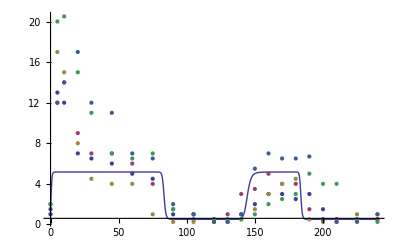

```mathematica
(*display Brown's model in transient*)
{aa,bb,mm,ss}=nlm["ParameterTableEntries"][[All,1]]
Pbrown[Y_]:=aa*ss^mm/(ss^mm+Y^mm)+bb
Show[Plot[Pbrown[Ca[t]/.Sol3[[1]][[1]]],{t,0,240},PlotRange->All],ListPlot[Prot3]]
```

```mathematica
(*MLE version of this model*)
(*each individual has one pair of cell types, not 20*)
{kv1,kd1,m1,kv2,kd2,m2,gammac,beta}=Mean[Table[Mean[PV[[i]]],{i,1,Length[PV]}]]
nds=NDSolve[{
SF1[t]==beta-((beta-gammac)*Ca[t]^m1/(Ca[t]^m1+kd1^m1)),
SF2[t]==beta-((beta-gammac)*Ca[t]^m2/(Ca[t]^m2+kd2^m2)),
P'[t]==(SF1[t]*V1[t]+SF2[t]*V2[t])-(kcl*P[t])-EP'[t],
P[0]==(kv1/kcl)*(beta-(beta-gammac)*ca0^m1/(ca0^m1+kd1^m1))/(kdeg+beta-(beta-gammac)*ca0^m1/(ca0^m1+kd1^m1))+(kv2/kcl)*(beta-(beta-gammac)*ca0^m2/(ca0^m2+kd2^m2))/(kdeg+beta-(beta-gammac)*ca0^m2/(ca0^m2+kd2^m2)),
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),
EP[0]==(11/SVol)*P[0],
V1'[t]==kv1-(kdeg+SF1[t])*V1[t],
V2'[t]==kv2-(kdeg+SF2[t])*V2[t],
V1[0]==(kv1/((beta+kdeg-(beta-gammac)*(ca0^m1)/(ca0^m1+kd1^m1)))),
V2[0]==(kv2/((beta+kdeg-(beta-gammac)*(ca0^m2)/(ca0^m2+kd2^m2)))),
Ca'[t]==Piecewise[{{0.175*(ca0-0.2-Ca[t]),t<75},{.075*(ca0+0.2-Ca[t]),75<=t<130},{.075*(ca0-0.12-Ca[t]),t<180},{.1*(ca0+0.2-Ca[t]),True}}],Ca[0]==ca0},
{P,Ca,V1,V2,EP,SF1,SF2},{t,0,240}]
```

{3.36174,1.1319,273.25,2.225,1.27584,235.478,0.00140533,0.498141}

{{P→InterpolatingFunction[{{0.,240.}},<>],Ca→InterpolatingFunction[{{0.,240.}},<>],V1→InterpolatingFunction[{{0.,240.}},<>],V2→InterpolatingFunction[{{0.,240.}},<>],EP→InterpolatingFunction[{{0.,240.}},<>],SF1→InterpolatingFunction[{{0.,240.}},<>],SF2→InterpolatingFunction[{{0.,240.}},<>]}}

```mathematica
(*residual testing*)
FitResiduals[data_,f_]:=Table[Abs[data[[i,2]]-(f)/.t->data[[i,1]]],{i,1,Length[data]}]

FitResidualsSingle=Apply[Plus,Flatten[FitResiduals[Prot3[[1]],(P[t]/3)/.nds]]]
FitResidualsBrown=Apply[Plus,Flatten[FitResiduals[Prot3[[1]],Pbrown[Ca[t]/.nds]]]]
FitResidualsMultiple=Apply[Plus,Flatten[FitResiduals[Prot3[[1]],Mean[P3]]]]
Print[]
ssFitResidualsSingle=Apply[Plus,Flatten[FitResiduals[Prot3[[1]],(P[t]/3)/.nds]]^2]
ssFitResidualsBrown=Apply[Plus,Flatten[FitResiduals[Prot3[[1]],Pbrown[Ca[t]/.nds]]]^2]
ssFitResidualsMultiple=Apply[Plus,Flatten[FitResiduals[Prot3[[1]],Mean[P3]]]^2]
```

53.954

33.9011

42.5466

310.719

147.547

115.06

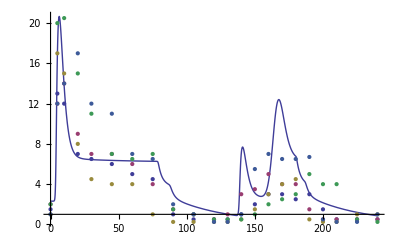

```mathematica
(*Plot of MLE version of model*)
Show[Plot[(P[t]/SVol)/.nds,{t,0,240},PlotRange->All],ListPlot[Prot3]]
TRange=Range[0,240];
psingle=(P[t]/SVol)/.nds/.t->TRange;
pbrown=Pbrown[Ca[t]/.Sol3[[1]][[1]]]/.t->TRange;
pmult=Mean[P3]/.t->TRange;
(*Export[path<>"comparison_exp.xlsx",Transpose[Join[{Prot3[[All,All,1]][[1]]},Table[Prot3[[All,All,2]][[i]],{i,1,Length[Prot3]}]]]]*)
```